# Parallelschwingkreis

## Funktionen

### Includes

```mathematica
<<"Labor.m"
```

```mathematica
Needs["ErrorBarPlots`"]
```

## Geräteliste

Oszi: HM400
true rms: Fluke 175

## 1.) Resonanzfrequenz (Bestimmung aus Amplituden- und Phasenverlauf

### Induktivität und Kapazität

```mathematica
l={3,0}*10^-3;
rl=0.5;
c={0.1,0.01}*10^-6;
```

### Theoretische Resonanzfrequenz

```mathematica
(Elec`Fω[l[[1]],l[[2]],c[[1]],c[[2]]])/(2*π)
```

{9188.81,459.441}

### Messung

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {42.9, 50*10^-3, 0.6*5*10^-3, 4}, {94.8, 1.7*50*10^-3, 2.1*10^-3, 2*2}, {204.2, 1.8*0.1, 2.2*0.5*10^-3, 2*2}, {438, 1.8*0.2, 0.5*10^-3, 4}, {1510, 2.6*0.5, 2.6*50*10^-6, 2*2}, {3016, 2.6*1, 1*50*10^-6, 2.2*2}, {4410, 3.6*1, 1.2*20*10^-6, 2.5*2}, {6750, 2.5*2, 0.4*20*10^-6, 2.8*2}, {7.08*10^3, 2.6*2, 0.6*10*10^-6, 2.9*2}, {8.17*10^3, 2.8*2, 1.2*2*10^-6, 3*2}, {9.36*10^3, 2.8*2, 0, 3*2}, {10.17*10^3, 2.8*2, -0.3*5*10^-6, 3*2}, {11.08*10^3, 2.7*2, -0.5*5*10^-6, 3*2}, {12.15*10^3, 2.9*2, -0.6*5*10^-6, 2.6*2}, {13.00*10^3, 2.5*2, -0.8*5*10^-6, 2.8*2}, {14.20*10^3, 2.4*2, -0.9*5*10^-6, 2.8*2}, {16.93*10^3, 2.1*2, -1*5*10^-6, 2.6*2}, {43.60*10^3, 3.4*0.5, -0.8*5*10^-6, 2*2}, {120.9*10^3, 2.9*0.2, -1.8*10^-6, 2*2}, {418.6*10^3, 1.2*0.1, -1.2*0.5*10^-6, 2*2}, {1012*10^3, 0.8*0.1, 1.1*0.2*10^-6, 2*2}}; dM={{"Δf/Hz", "ΔU/V", "Δδt"}, {□, 50*10^-3, 5*10^-3}, {□, 0.2, 0.5}, {□, 1, 1}, {1, 1, 1}, {1, 1, 1}, {1, 1, 1}, {1, 1, 1}, {1, 1, 1}, {1, 1, 1}, {1, 1, 1}, {1, 1, 1}, {1, 1, 1}};
Ue=4;(*eff, fluke 175*)
due=2/5;
```

### Amplitudengang

```mathematica
{M[[2;;Length[M],1]],M[[2;;Length[M],2]]}
```

{{42.9,94.8,204.2,438,1510,3016,4410,6750,7080.,8170.,9360.,10170.,11080.,12150.,13000.,14200.,16930.,43600.,120900.,418600.,1012000},{1/20,0.085,0.18,0.36,1.3,2.6,3.6,5.,5.2,5.6,5.6,5.6,5.4,5.8,5.,4.8,4.2,1.7,0.58,0.12,0.08}}

```mathematica
(*ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,AxesLabel-> {"f/Hz","Ua/Ue"}]*)
```

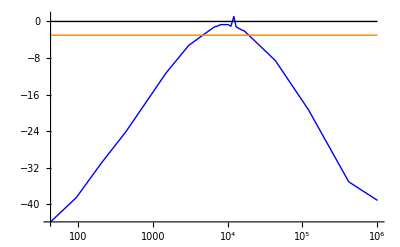

```mathematica
Show[ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,PlotStyle-> {Blue}],LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}]]
```

### Phasengang

```mathematica
(*ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}]*)
```

```mathematica
(*p1 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,3]],ϕ[[x-1,2]]]},{x,2,Length[M]}];*)
```

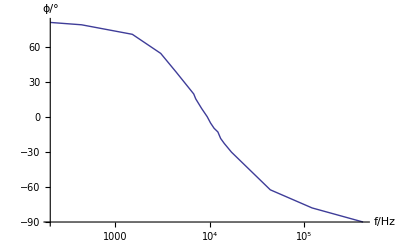

```mathematica
p2=Table[{M[[x,1]],M[[x,1]]*M[[x,3]]*360},{x,4,Length[M]-1}];
ListLogLinearPlot[p2,AxesLabel-> {"f/Hz","ϕ/°"},Joined-> True(*,PlotRange-> {{0,10^6},{-90,90}}*)]
```